# 11. Strings and Text

```mathematica
"This is a string"
```

```mathematica
"This is a string"
```

This is a string

```mathematica
StringLength["This is a string"]
```

16

```mathematica
StringReverse["This is a string"]
```

gnirts a si sihT

```mathematica
?String*
```

```mathematica
ToUpperCase["This is a string"]
```

THIS IS A STRING

```mathematica
ToLowerCase[%]
```

this is a string

```mathematica
StringTake[%, 4]
```

this

```mathematica
StringJoin["this"," is it"]
```

this is it

```mathematica
StringJoin[{"wow ", "lists, ", "cool"}]
```

wow lists, cool

```mathematica
list={"wow ", "lists, ", "cool"}
```

{wow ,lists, ,cool}

```mathematica
StringTake[list,2]
```

{wo,li,co}

```mathematica
StringJoin[%,%]
```

wow lists, coolwow lists, coolwow lists, coolwow lists, coolwow lists, coolwow lists, coolwow lists, coolwow lists, coolwow lists, coolwow lists, coolwow lists, coolwow lists, coolwow lists, coolwow lists, coolwow lists, coolwow lists, coolwow lists, coolwow lists, coolwow lists, coolwow lists, coolwow lists, coolwow lists, coolwow lists, coolwow lists, coolwow lists, coolwow lists, coolwow lists, coolwow lists, coolwow lists, coolwow lists, coolwow lists, coolwow lists, cool

```mathematica
"wow lists, coolwow lists, cool"
```

wow lists, coolwow lists, cool

```mathematica
Characters[list]
```

{{w,o,w, },{l,i,s,t,s,,, },{c,o,o,l}}

```mathematica
Sort[%]
```

{{c,o,o,l},{w,o,w, },{l,i,s,t,s,,, }}

```mathematica
Sort[Flatten[%]]
```

{,, , ,c,i,l,l,o,o,o,s,s,t,w,w}

```mathematica
TextWords["This is a sentence. Sentences are cool. А? Чё звал сларк."]
```

{This,is,a,sentence,Sentences,are,cool,А,Чё,звал,сларк}

```mathematica
{"This","is","a","sentence","Sentences","are","cool"
```

{This,is,a,sentence,Sentences,are,cool}

```mathematica
WikipediaData["9/11"]
```

```mathematica
DeleteStopwords[%]
```

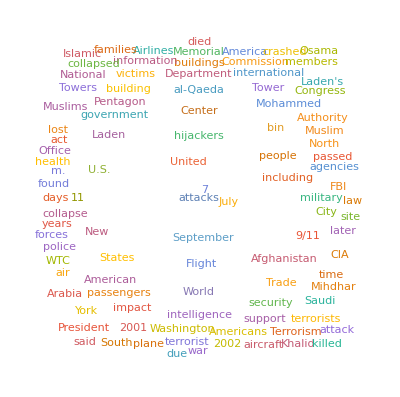

```mathematica
WordCloud[%]
```

```mathematica
WordList[]
```

```mathematica
WordList[]
```

```mathematica
Remove["Global`*"]
```

Remove::rmnsm: There are no symbols matching "Global`*".

```mathematica
Take[WordList[],100]
```

{a,aah,aardvark,aback,abacus,abaft,abalone,abandon,abandoned,abandonment,abase,abasement,abash,abashed,abashment,abate,abatement,abattoir,abbe,abbess,abbey,abbot,abbreviate,abbreviated,abbreviation,abdicate,abdication,abdomen,abdominal,abduct,abducting,abduction,abductor,abeam,abed,aberrant,aberration,abet,abettor,abeyance,abhor,abhorrence,abhorrent,abidance,abide,abiding,ability,abject,abjection,abjectly,abjuration,abjure,ablate,ablated,ablation,ablative,ablaze,able,abloom,ablution,ably,abnegate,abnegation,abnormal,abnormality,abnormally,aboard,abode,abolish,abolition,abolitionism,abolitionist,abominable,abominably,abominate,abomination,aboriginal,aborigine,abort,abortion,abortionist,abortive,abortively,abound,abounding,about,above,aboveboard,abracadabra,abrade,abrasion,abrasive,abrasiveness,abreast,abridge,abridged,abridgment,abroad,abrogate,abrogation}

```mathematica
RomanNumeral[500]
```

D

```mathematica
RomanNumeral[44444]
```

"XL" _MMMMCDXLIV

```mathematica
Alphabet["Japanese"]
```

Alphabet::noalpha: The alphabet Japanese is not known or not available.

Alphabet[Japanese]

```mathematica
WikipediaData["9/11"]//TextWords //Length
```

14169

```mathematica
WikipediaData["Moldova"]//TextWords //Length
```

11877

```mathematica
WordList[]//StringLength//Max
```

23

```mathematica
Select[WordList[], StringLength[#]==23&]
```

{electroencephalographic}

```mathematica
Alphabet["English"]//Length
```

26

```mathematica
Table[RandomInteger[25]+1//FromLetterNumber,1000]
```

{x,d,b,w,q,e,r,v,t,e,c,m,g,r,x,v,y,g,c,n,s,r,a,j,p,x,m,i,v,r,h,w,r,q,d,y,j,i,f,d,s,d,w,a,h,j,j,c,y,c,f,q,a,r,g,q,x,u,s,z,k,y,h,p,j,o,b,k,x,k,d,x,u,g,t,y,t,h,w,b,m,v,c,f,i,j,s,f,c,e,y,x,b,y,e,t,a,m,t,i,r,s,r,a,r,m,l,x,f,j,v,n,f,k,j,u,t,z,o,p,t,c,h,p,t,k,t,v,p,z,n,x,m,n,v,r,j,c,c,m,z,q,o,u,d,p,w,l,y,p,g,z,o,l,z,q,d,h,a,l,z,m,y,b,i,e,f,l,b,c,k,n,r,d,q,s,o,q,i,o,j,v,n,h,l,w,j,v,q,c,p,d,w,g,c,j,t,e,d,i,h,c,a,d,j,g,p,x,a,w,q,p,s,f,z,s,c,n,e,i,l,q,e,j,j,n,x,m,x,l,m,x,i,c,n,e,u,j,e,u,f,b,w,m,p,o,l,k,h,y,n,r,t,s,m,b,v,i,g,c,o,m,h,w,n,f,a,g,t,e,u,j,f,n,o,x,r,t,v,y,j,x,q,m,u,q,q,t,s,h,b,t,u,l,m,a,d,k,w,e,h,e,m,l,h,q,g,x,n,a,n,l,g,e,o,c,c,t,r,s,d,x,h,t,z,v,k,o,o,v,i,w,l,f,s,m,p,u,b,i,u,b,e,x,e,y,k,g,y,r,p,x,s,l,e,c,v,i,d,x,n,i,q,a,d,g,e,d,b,g,q,k,h,q,f,d,j,n,n,x,c,s,x,h,r,a,c,s,c,s,w,k,g,n,a,s,j,k,w,w,u,y,k,v,g,v,d,y,w,k,u,j,x,j,i,l,o,h,e,r,e,e,g,y,w,v,u,t,j,n,t,l,t,m,k,u,o,m,q,z,l,s,r,k,i,s,a,p,q,h,v,v,g,h,w,j,s,a,m,x,t,a,r,g,n,m,n,i,b,j,m,l,n,t,j,m,v,v,n,l,e,d,d,l,h,k,t,x,j,c,c,j,t,b,r,k,u,i,r,d,k,q,x,a,l,j,m,w,l,p,z,l,p,h,j,b,s,m,g,s,o,x,v,m,e,c,l,l,n,v,v,i,c,p,m,a,y,w,m,t,e,q,x,q,k,h,o,r,r,z,u,x,y,l,v,e,h,v,c,c,e,m,e,a,d,z,d,p,n,y,q,q,n,s,o,k,c,a,k,f,f,z,x,k,g,b,b,x,o,u,y,x,v,n,y,x,r,f,h,s,z,r,y,u,x,q,c,x,h,s,h,l,c,p,f,d,j,w,m,n,t,l,z,x,j,o,p,b,w,j,o,s,n,a,n,n,l,p,t,k,h,j,m,b,o,o,b,d,b,z,p,r,t,q,a,c,w,v,x,n,j,q,o,k,o,r,a,b,g,b,j,f,i,n,o,m,l,x,s,m,b,o,s,y,u,i,e,x,k,g,h,m,y,u,f,a,n,n,t,n,g,g,l,o,q,j,m,z,b,i,j,k,l,p,l,o,w,y,w,q,u,r,p,y,k,g,b,t,q,l,q,v,w,g,j,c,n,m,u,g,q,w,c,a,u,k,y,o,c,c,s,z,n,v,v,d,l,n,b,a,q,z,n,q,a,q,g,k,d,y,b,m,z,o,g,r,q,m,e,n,z,s,c,p,b,u,k,d,y,v,b,h,i,m,n,e,w,g,m,a,k,w,v,a,n,r,b,a,q,p,u,a,k,s,a,s,x,c,a,w,n,y,l,j,h,t,z,m,y,f,w,h,e,a,i,k,o,a,j,m,p,t,n,o,n,f,b,u,f,n,b,j,f,u,x,j,a,j,f,n,v,p,u,z,o,f,u,q,y,l,h,k,a,p,r,p,e,p,f,l,s,x,q,w,a,i,b,s,u,g,m,v,o,y,c,p,j,f,u,r,g,i,c,g,f,w,i,p,v,w,j,d,n,r,x,k,l,j,a,h,d,w,b,l,o,e,k,p,y,n,c,x,c,q,p,m,k,b,y,u,k,j,x,v,g,q,h,e,p,q,g,i,w,y,a,o,x,m,e,i,r,s,l,b,u,s,y,w,k,r,c,z,k,d,m,y,c,l,z,n,g,v,y,p,e,u,o,z,h,v,k,u,x,p,q,n,p,b,o,b}

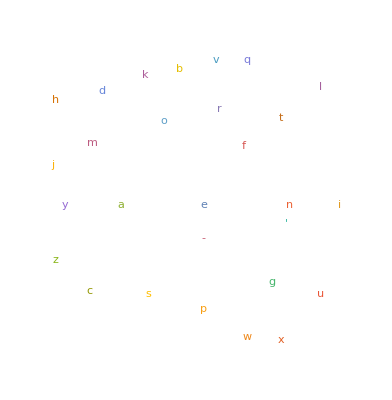

```mathematica
WordList[]//Characters//WordCloud
```

```mathematica
RandomInteger[1000,{1000, 3}]//ListPointPlot3D
```

-Graphics3D-

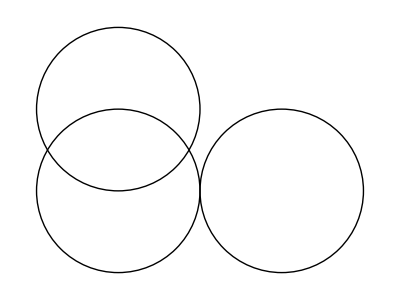

```mathematica
Graphics[{Circle[{1,1}],Circle[{1,2}],Circle[{3,1}]}]
```

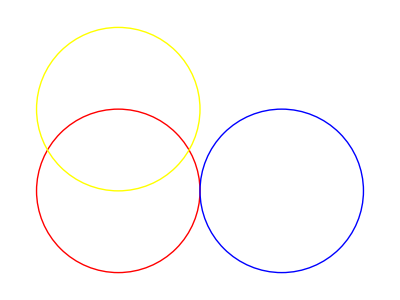

```mathematica
Graphics[{Style[Circle[{1,1}],Red],Style[Circle[{1,2}],Yellow],Style[Circle[{3,1}],Blue]}]
```

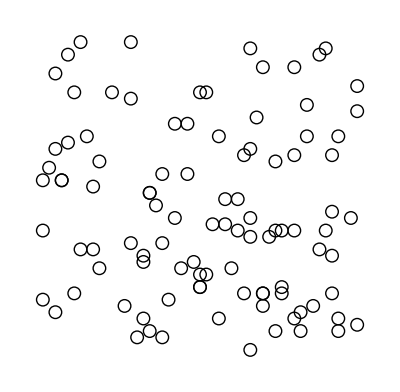

```mathematica
Graphics[Table[Circle[RandomInteger[50,2]],100]]
```

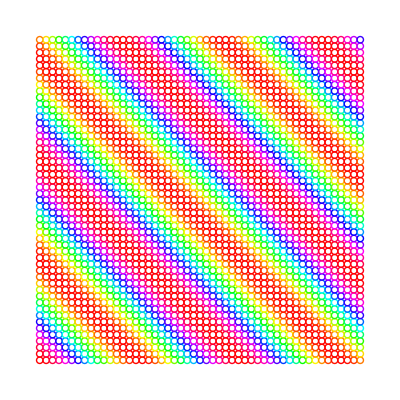

```mathematica
Table[Style[Circle[{x,y}],Hue[(Cos[(x+y)/10]+1)/2]],{x,0,100,2},{y,0,100,2}]//Graphics
```

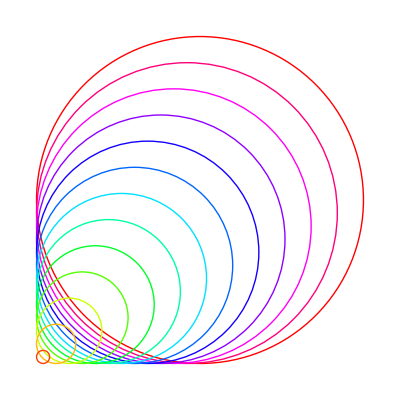

```mathematica
Table[Style[Circle[{r,r},r],Hue[r/10]],{r,10,0,-4/5}]//Graphics
```

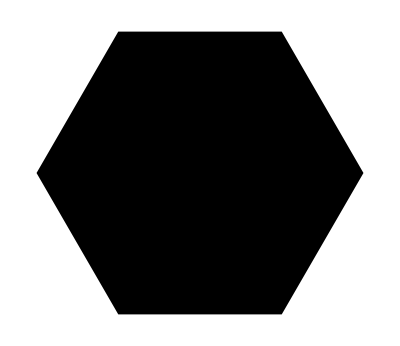

```mathematica
RegularPolygon[6]//Graphics
```

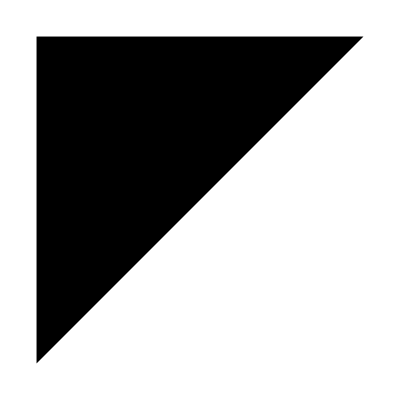

```mathematica
Graphics[Polygon[{{0,0},{1,1},{0,1}}]]
```

```mathematica
Graphics3D[Polyhedron[{{0.,0.,0.6},{-0.3,-0.5,-0.2},{-0.3,0.5,-0.2},{0.6,0.,-0.2}},{{2,3,4},{3,2,1},{4,1,2},{1,4,3}}]]
```

-Graphics3D-

```mathematica
Table[Style[Sphere[{x,y,z},1/2],Hue[x/5,y/5,z/5]],{x,5},{y,5},{z,5}]//Graphics3D
```

-Graphics3D-

```mathematica
n=8;
Table[Style[Point[{x,y,z}],Hue[x/n,y/n,z/n]],{x,n},{y,n},{z,n}]//Graphics3D
```

-Graphics3D-

```mathematica
Manipulate[Graphics3D[{Sphere[{0,0,0}], Style[Sphere[{x,0,0}],Opacity[o]]}],{x,0.1, 5}, {o,0.05,1}]
```

```mathematica
10x 10 by 1 centered in int coords
```

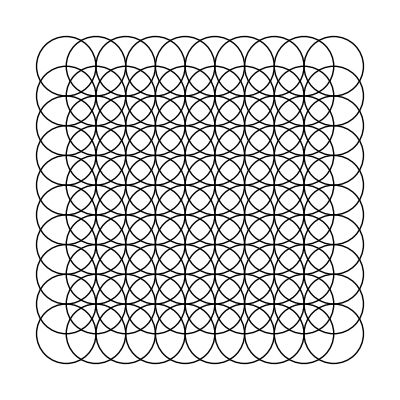

```mathematica
Table[Circle[{x,y}],{x,10},{y,10}]//Graphics
```

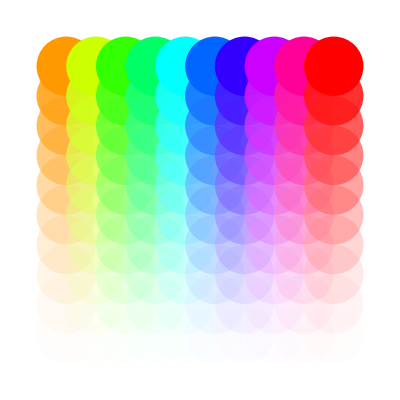

```mathematica
Table[Style[Disk[{x,y}],Hue[x/10,y/10, 1, y/10]],{x,10},{y,10}]//Graphics
```

```mathematica
(*1000 spheres rgb*)
Table[Style[Sphere[{x,y,z}],RGBColor[x/10,y/10,z/10,(x*y*z)/1000]],{x,10},{y,10},{z,10}]//Graphics3D
```

-Graphics3D-